## Analytical sol, up to calibration

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
startTime=AbsoluteTime[];

(* Needs ItosLemma package, https://library.wolfram.com/infocenter/ID/1170/ *)

<<ItosLemma`
Clear[t, dt, dB, ρ, μ, σ];
{TimeSymbol, TimeIncrement, BrownianIncrement, CorrelationSymbol,
	DriftSymbol, DiffusionSymbol} = {t, dt, dB, ρ, μ, σ};
```

Order of Brownians:
Bδ is B1
Bπ is B2
By is B3
Ba is B4

```mathematica
(*c is log[δ]*)
ChangeItoBack={δ->δt,c->ct,ππ->ππt,y->yt,a->at,d->dt,ϕ->ϕt};
ChangeIto2={δ[t]->δ,c[t]->c,ππ[t]->ππ,y[t]->y,a[t]->a,d[t]->d};
(*Output*)
dδ=ItoMake[δ[t],μδt δ[t],{σδ δ[t],0,0,0}] 
(*Log consumption*)
dc=ItoMakeFromItoD[c[t],ItoD[Log[δ[t]],SuppressTime->False]]
(* Output gap *)
dy=ItoMake[y[t],-λy y[t],{0,0,σy,0}]
```

dt μδt δ[t]+σδ dB_1 δ[t]

dt (μδt-σδ^2/2)+σδ dB_1

σy dB_3-dt λy y[t]

```mathematica
(*Taylor rule, based on inflation and output gap*)
replrN={rNt->rNbar+βπ(ππ[t]-πbar)+βy y[t]};

πtA=πbar-a[t] (rNt-rNbar)/.replrN;
dππ=ItoMake[ππ[t],λπ (πtA-ππ[t]),{0,σπ,0,0}]
daInitial=ItoMake[a[t],-λa a[t],{0,0,0,σa}]
```

σπ dB_2+dt λπ (πbar-ππ[t]-a[t] (βy y[t]+βπ (-πbar+ππ[t])))

-dt λa a[t]+σa dB_4

```mathematica
(* Monetay Policy Stance *)
replaceyWithϕ=Solve[ϕ==βπ(ππ-πbar)+βy y,y]//Flatten
replaceππWithϕ=Solve[ϕ==βπ(ππ-πbar)+βy y,ππ]//Flatten;
dϕ=ItoD[βπ(ππ[t]-πbar)+βy y[t]]/.replaceyWithϕ/.{ππ->ππ[t],ϕ->ϕ[t],a->a[t]}//FullSimplify
```

{y→(βπ πbar-βπ ππ+ϕ)/βy}

βπ σπ dB_2+βy σy dB_3-dt βπ (λy-λπ) (πbar-ππ[t])-dt (λy+βπ λπ a[t]) ϕ[t]

Learnig

```mathematica
$Assumptions={σπ>0,ψ>1};

A0={{λπ (πbar-ππt)}};
A1={{-λπ ϕt}};
B1={{0}};
B2={{σπ}};
a0={{0}};
a1={{-λa}};
b1={{σa}};
b2={{0}};
bob=b1.Transpose[b1]+b2.Transpose[b2]//FullSimplify;
BoB=B1.Transpose[B1]+B2.Transpose[B2]//FullSimplify;
boB=b1.Transpose[B1]+b2.Transpose[B2]//FullSimplify;
LS=(boB+νa[t]Transpose[A1]).Inverse[BoB]//FullSimplify
```

{{-(λπ ϕt νa[t])/σπ^2}}

Dynamics of the posterior variance

```mathematica
condν=a1 νa[t]+νa[t]Transpose[a1]+bob-LS.Transpose[boB+νa[t]Transpose[A1]]//FullSimplify
```

{{σa^2-2 λa νa[t]-(λπ^2 ϕt^2 νa[t]^2)/σπ^2}}

Steady-state Bayesian uncertainty.

```mathematica
condνaSS=condν[[1,1]]/.{ϕt->0}/.νa[t]->νat//Simplify
replaceνss=Solve[condνaSS==0,νat]//Flatten//Simplify
solνss=νat/.replaceνss
```

-2 λa νat+σa^2

{νat→σa^2/(2 λa)}

σa^2/(2 λa)

Get Independent Brownians under observation filtration
(this step doesn’t change anything, because we assume Brownians are uncorrelated)

```mathematica
CorrelatedBrown=Join[B1,B2,2]//FullSimplify;
CorrelatedBrown//MatrixForm;
varcovmatBrownvec=CorrelatedBrown.Transpose[CorrelatedBrown]//FullSimplify;
varcovmatBrownvec//MatrixForm;
DiffObservedVec=Transpose[CholeskyDecomposition[varcovmatBrownvec]]//FullSimplify;
DiffObservedVec//MatrixForm;

DiffFilter=LS.DiffObservedVec//FullSimplify;
DiffFilter//MatrixForm
```

(-(λπ ϕt νa[t])/σπ)

Fix ν_a,t to its steady-state value multiplied by a constant, calibfactorν (to be calibrated)

```mathematica
(*filtered a*)
da=ItoMake[a[t],-λa a[t],{0,-((rNt-rNbar) λπ solνss calibfactorν)/σπ,0,0,0}]
```

-dt λa a[t]-(calibfactorν (-rNbar+rNt) λπ σa^2 dB_2)/(2 λa σπ)

```mathematica
(*HJB Equation. Equation with WC=Log[wealth-consumption] ratio, I(x_t) in the paper*)
Jfunc= Exp[c[t]]^(1-γ)/(1-γ)(ρ Exp[WC[ππ[t],a[t],y[t]]])^((1-γ)/(1-1/ψ));
aggregator=ρ(1-γ)/(1-1/ψ)Jfunc((Exp[c]/((1-γ)Jfunc)^(1/(1-γ)))^(1-1/ψ)-1)/.ChangeIto2;
LJ=Drift[ItoD[Jfunc]]//FullSimplify;
HJB=(aggregator+LJ)/(Exp[c]^(1-γ)/(1-γ)(ρ Exp[WC[ππ,a,y]])^((1-γ)/(1-1/ψ)))//PowerExpand//Simplify
```

1/8 (1-γ) (8 μδt-4 γ σδ^2-(8 (ⅇ^(-WC[ππ,a,y])-ρ) ψ)/(1-ψ)-(8 y λy ψ WC^(0,0,1)[ππ,a,y])/(-1+ψ)-(4 (-1+γ) σy^2 ψ^2 (WC^(0,0,1)[ππ,a,y])^2)/(-1+ψ)^2+(4 σy^2 ψ WC^(0,0,2)[ππ,a,y])/(-1+ψ)+1/(λa^2 σπ^2 (-1+ψ)^2)ψ (-calibfactorν^2 (rNbar-rNt)^2 (-1+γ) λπ^2 σa^4 ψ (WC^(0,1,0)[ππ,a,y])^2+calibfactorν^2 (rNbar-rNt)^2 λπ^2 σa^4 (-1+ψ) WC^(0,2,0)[ππ,a,y]+4 λa σπ^2 WC^(0,1,0)[ππ,a,y] (-2 a λa^2 (-1+ψ)-calibfactorν (rNbar-rNt) (-1+γ) λπ σa^2 ψ WC^(1,0,0)[ππ,a,y])+4 λa σπ^2 (-2 λa λπ (a y βy-πbar+ππ+a βπ (-πbar+ππ)) (-1+ψ) WC^(1,0,0)[ππ,a,y]-(-1+γ) λa σπ^2 ψ (WC^(1,0,0)[ππ,a,y])^2+(-1+ψ) (calibfactorν (rNbar-rNt) λπ σa^2 WC^(1,1,0)[ππ,a,y]+λa σπ^2 WC^(2,0,0)[ππ,a,y]))))

```mathematica
(*For PDE in paper*)
repγ=Solve[(1-γ)/(1-1/ψ)==θ,γ]//Flatten//FullSimplify
repψ={ψ->θ/(θ-1+γ)};
repθ={θ->(1-γ)/(1-1/ψ)};
CoefficientArrays[HJB,{Derivative[1,0,0][WC][ππ,a,y],Derivative[0,1,0][WC][ππ,a,y],Derivative[0,0,1][WC][ππ,a,y],Derivative[2,0,0][WC][ππ,a,y],Derivative[0,2,0][WC][ππ,a,y],Derivative[0,0,2][WC][ππ,a,y],Derivative[1,1,0][WC][ππ,a,y]}]//Normal//FullSimplify;
HJBcoeffs=%/θ/.repψ/.calibfactorν->νa/solνss//FullSimplify;
Style[HJBcoeffs[[1]],Background->Yellow]
Style[HJBcoeffs[[2]]//MatrixForm,Background->Yellow]
Style[HJBcoeffs[[3]]//MatrixForm,Background->Yellow]
```

{γ→1+θ (-1+1/ψ)}

ⅇ^(-WC[ππ,a,y])-ρ+((-1+γ) (-2 μδt+γ σδ^2))/(2 θ)

(-λπ (a y βy-πbar+ππ+a βπ (-πbar+ππ))
-a λa
-y λy
σπ^2/2
((rNbar-rNt)^2 λπ^2 νa^2)/(2 σπ^2)
σy^2/2
(rNbar-rNt) λπ νa)

((θ σπ^2)/2 | (rNbar-rNt) θ λπ νa | 0 | 0 | 0 | 0 | 0
0 | ((rNbar-rNt)^2 θ λπ^2 νa^2)/(2 σπ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | (θ σy^2)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
HJBcoefWC2=CoefficientList[HJB,Derivative[2,0,0][WC][ππ,a,y]]//Simplify;
%//Dimensions
repWC2f={Derivative[2,0,0][WC][ππ,a,y]->-HJBcoefWC2[[1]]/HJBcoefWC2[[2]]}//Simplify;
(*REMARK: To get rid of all of the previous $Assumptions, set Assumptions->True in Solve*)
repWC2f$1=Solve[HJB==0,Derivative[2,0,0][WC][ππ,a,y],Assumptions->True]//Flatten//Simplify;
(* verification *)
(Derivative[2,0,0][WC][ππ,a,y]/.repWC2f)-(Derivative[2,0,0][WC][ππ,a,y]/.repWC2f$1)//Simplify
```

{2}

0

```mathematica
sdf=Exp[∫_0^t ((θ-1)/Exp[WC[ππ[s],a[s],y[s]]]-ρ θ)ⅆs] ρ^θ Exp[c[t]]^-γ Exp[WC[ππ[t],a[t],y[t]]]^(θ-1);

(* The above has been verified by computing derivatives of the function h. See also Appendix B. *)

rfrate=-Drift[ItoD[sdf]]/sdf/.ChangeIto2/.repWC2f/.{θ->(1-γ)/(1-1/ψ)}//FullSimplify

MPR=Transpose[{-Diffusion[ItoD[sdf],BrownianList->{Subscript[dB, 1],Subscript[dB, 2],Subscript[dB, 3],Subscript[dB, 4]}]/sdf}]/.ChangeIto2/.repWC2f/.{θ->(1-γ)/(1-1/ψ)}//FullSimplify
```

ρ+(2 μδt-γ σδ^2 (1+ψ))/(2 ψ)-1/(8 λa^2 σπ^2 (-1+ψ))(-1+γ ψ) (4 λa^2 σy^2 σπ^2 (WC^(0,0,1)[ππ,a,y])^2+(calibfactorν (rNbar-rNt) λπ σa^2 WC^(0,1,0)[ππ,a,y]+2 λa σπ^2 WC^(1,0,0)[ππ,a,y])^2)

{{γ σδ},{((-1+γ ψ) (calibfactorν (rNbar-rNt) λπ σa^2 WC^(0,1,0)[ππ,a,y]+2 λa σπ^2 WC^(1,0,0)[ππ,a,y]))/(2 λa σπ (-1+ψ))},{(σy (-1+γ ψ) WC^(0,0,1)[ππ,a,y])/(-1+ψ)},{0}}

```mathematica
MPRforpaper=Transpose[{-Diffusion[ItoD[sdf],BrownianList->{Subscript[dB, 1],Subscript[dB, 2],Subscript[dB, 3],Subscript[dB, 4]}]/sdf}]/.ChangeIto2/.repWC2f/.calibfactorν->νa(2 λa)/σa^2//FullSimplify
rfrateforpaper=rfrate/.calibfactorν->νa/solνss//FullSimplify
(-1+γ ψ)/(-1+ψ)==1-(1-γ)/(1-1/ψ)//Simplify
```

{{γ σδ},{-((-1+θ) (((rNbar-rNt) λπ νa WC^(0,1,0)[ππ,a,y])/σπ+σπ WC^(1,0,0)[ππ,a,y]))},{-((-1+θ) σy WC^(0,0,1)[ππ,a,y])},{0}}

ρ+(2 μδt-γ σδ^2 (1+ψ))/(2 ψ)-((-1+γ ψ) (σy^2 σπ^2 (WC^(0,0,1)[ππ,a,y])^2+((rNbar-rNt) λπ νa WC^(0,1,0)[ππ,a,y]+σπ^2 WC^(1,0,0)[ππ,a,y])^2))/(2 σπ^2 (-1+ψ))

True

```mathematica
wealth=δ[t]Exp[WC[ππ[t],a[t],y[t]]];
wealthdiff={Diffusion[ItoD[wealth]/wealth,BrownianList->{Subscript[dB, 1],Subscript[dB, 2],Subscript[dB, 3],Subscript[dB, 4]}]}/.ChangeIto2//FullSimplify
wealthVar=(wealthdiff.Transpose[wealthdiff])[[1,1]]//FullSimplify
wealthdiffforpaper={Diffusion[ItoD[wealth]/wealth,BrownianList->{Subscript[dB, 1],Subscript[dB, 2],Subscript[dB, 3],Subscript[dB, 4]}]}/.ChangeIto2//FullSimplify;
```

{{σδ,(calibfactorν (rNbar-rNt) λπ σa^2 WC^(0,1,0)[ππ,a,y])/(2 λa σπ)+σπ WC^(1,0,0)[ππ,a,y],σy WC^(0,0,1)[ππ,a,y],0}}

σδ^2+σy^2 (WC^(0,0,1)[ππ,a,y])^2+((calibfactorν (rNbar-rNt) λπ σa^2 WC^(0,1,0)[ππ,a,y])/(2 λa σπ)+σπ WC^(1,0,0)[ππ,a,y])^2

```mathematica
rfrateNoσW2=rfrate+(-1+γ ψ)/(2(-1+ψ))wealthVar//FullSimplify;
CoefficientArrays[rfrateNoσW2,{ρ,μδt,σδ}]//Normal//FullSimplify;
Style[%,Background->Yellow]
(γ-ψ)/(2 (-1+ψ) ψ)/.repγ//FullSimplify
%/.{θ->1,ψ->1/γ}//FullSimplify
(γ (1+ψ))/(2 ψ)/.{ψ->1/γ}//FullSimplify
(* Verification of the real risk-free rate in the paper *)
ρ+μδt/ψ-(γ (1+ψ))/(2 ψ)σδ^2-(1-θ)/2(wealthVar-σδ^2)-rfrate/.repθ//FullSimplify
```

{0,{1,1/ψ,0},{{0,0,0},{0,0,0},{0,0,(γ-ψ)/(2 (-1+ψ) ψ)}}}

-(θ+ψ)/(2 ψ^2)

-1/2 γ (1+γ)

1/2 γ (1+γ)

0

```mathematica
(*Nominal risk-free rate*)
rfnominal=rfrate+ππ/.replrN/.ChangeIto2;
(*Replace steady-state values in derivatives driving rfnominal
Remark: This is the APPROXIMATE expected value of rfnominal assuming the derivatives are constant, i.e., assuming WC is affine*)
replrNbar={rNbar->rfnominal/.{Derivative[1,0,0][WC][ππ,a,y]->DπWCss,Derivative[0,0,1][WC][ππ,a,y]->DyWCss}/.{ππ->πbar,μδt->μbar,a->0,y->0}}//Simplify;

rNbarforpaper=rNbar/.replrNbar//FullSimplify

(*Equilibrium real expected growth rate μδ *)
replμδ=Solve[rfnominal==(rNt/.replrN/.ChangeIto2),μδt,Assumptions->True] //FullSimplify//Flatten;

μδforpaper=μδt/.replμδ/.calibfactorν->νa/solνss/.{y βy->(rNt-rNbar)-βπ (ππ-πbar)}//FullSimplify

(*sol for μδ with CRRA utility*)
rfnominalCRRA=rfnominal/.ψ->1/γ//Simplify;
replμδCRRA=Solve[rfnominalCRRA==(rNt/.replrN/.ChangeIto2),μδt,Assumptions->True] //Flatten//Simplify;

(*Check that it matches with CRRA utility*)
(μδt/.replμδ/.ψ->1/γ//Simplify)-(μδt/.replμδCRRA)//Flatten//Simplify
```

πbar+ρ-((DyWCss^2 σy^2+DπWCss^2 σπ^2) (-1+γ ψ))/(2 (-1+ψ))+(2 μbar-γ σδ^2 (1+ψ))/(2 ψ)

1/2 (2 (rNt-ππ-ρ) ψ+γ σδ^2 (1+ψ)+(ψ (-1+γ ψ) (σy^2 σπ^2 (WC^(0,0,1)[ππ,a,y])^2+((rNbar-rNt) λπ νa WC^(0,1,0)[ππ,a,y]+σπ^2 WC^(1,0,0)[ππ,a,y])^2))/(σπ^2 (-1+ψ)))

0

```mathematica
CoefficientArrays[rNbar/.replrNbar,{DπWCss,DyWCss}]//Normal//FullSimplify;
Style[%,Background->Yellow]
(* Verification of rNbar in the paper *)
ρ+πbar+μbar/ψ-(γ (1+ψ))/(2 ψ)σδ^2-(1-θ)/2(σπ^2 DπWCss^2+σy^2 DyWCss^2)-(rNbar/.replrNbar)/.repθ//FullSimplify
```

{πbar+ρ+(2 μbar-γ σδ^2 (1+ψ))/(2 ψ),{0,0},{{-(σπ^2 (-1+γ ψ))/(2 (-1+ψ)),0},{0,-(σy^2 (-1+γ ψ))/(2 (-1+ψ))}}}

0

```mathematica
(* This is how μδt depends on the real risk-free rate and on WC derivatives *)
μδtFrf=Solve[rfrate==rf,μδt]//Flatten//FullSimplify;
CoefficientArrays[μδt/.μδtFrf,{Derivative[1,0][WC][ππ,y],Derivative[0,1][WC][ππ,y]}]//Normal//FullSimplify;
Style[%,Background->Yellow]

(* Verification of the expected growth rate μδt *)
ψ(rf-ρ)+(γ (1+ψ))/2 σδ^2+(ψ(1-θ))/2(wealthVar-σδ^2)-(μδt/.μδtFrf)/.repθ//FullSimplify
```

{rf ψ-ρ ψ+1/2 γ σδ^2 (1+ψ)+1/(8 λa^2 σπ^2 (-1+ψ))ψ (-1+γ ψ) (4 λa^2 σy^2 σπ^2 (WC^(0,0,1)[ππ,a,y])^2+(calibfactorν (rNbar-rNt) λπ σa^2 WC^(0,1,0)[ππ,a,y]+2 λa σπ^2 WC^(1,0,0)[ππ,a,y])^2)}

0

## Calibration & Numerical Solution

```mathematica
(*REMARK*)
(*The values for μbar and ρ are those needed to get rNbar=0.0444 as in the data.
That is our target nominal risk-free rate*)

calibration1={σδ->0.0212,σy->0.0215,λy->0.4219,βπ->0.4666,βy->0.1332,σπ->0.0131,πbar->0.0338,λπ->0.2436,σa->0.7434,λa->0.9365,μbar->0.025,ρ->0.0095,γ->10,ψ->2};
Meanν=0.28; (*check this value in Matlab estimation code*)
calibfactorνVal=Meanν/solνss/.calibration1

(* Double the uncertainty for the dashed lines in Figure 5 *)
(*calibfactorνVal=2Meanν/solνss/.calibration1*)

calibration=AppendTo[calibration1,calibfactorν->calibfactorνVal]

PDE=HJB/.replrN/.replμδ/.replrNbar/.ChangeIto2/.calibration;
```

0.948966

{σδ→0.0212,σy→0.0215,λy→0.4219,βπ→0.4666,βy→0.1332,σπ→0.0131,πbar→0.0338,λπ→0.2436,σa→0.7434,λa→0.9365,μbar→0.025,ρ→0.0095,γ→10,ψ→2,calibfactorν→0.948966}

```mathematica
multipbounds=4;

πminC=πbar-multipbounds √(σπ^2/(2 λπ))/.calibration;
πmaxC=πbar+multipbounds √(σπ^2/(2 λπ))/.calibration;
aminC=0-multipbounds √(σa^2/(2 λa))/.calibration;
amaxC=0+multipbounds √(σa^2/(2 λa))/.calibration;
yminC=0-multipbounds √(σy^2/(2 λy)) /.calibration;
ymaxC=0+multipbounds √(σy^2/(2 λy))/.calibration;
{{πminC,πmaxC},{aminC,amaxC},{yminC,ymaxC}}//MatrixForm

n=2; (*starting number of polynomials *)
nTot=4;(* total number of polynomials: *)
m=5;(*nb of interpolation nodes: works with 4, 5, 11, .... *)

(*Compute bounds to match chosen Chebyshev bounds*)
SolBounds=Solve[{(-Cos[1/(2m)π]+1)((UP-LOW)/2)+LOW==ChosenLow,(-Cos[(2m-1)/(2m)π]+1)((UP-LOW)/2)+LOW==ChosenUp},{UP,LOW}]//Flatten//Simplify;
πmax=UP/.SolBounds/.{ChosenLow->πminC,ChosenUp->πmaxC};
πmin=LOW/.SolBounds/.{ChosenLow->πminC,ChosenUp->πmaxC};
amax=UP/.SolBounds/.{ChosenLow->aminC,ChosenUp->amaxC};
amin=LOW/.SolBounds/.{ChosenLow->aminC,ChosenUp->amaxC};
ymax=UP/.SolBounds/.{ChosenLow->yminC,ChosenUp->ymaxC};
ymin=LOW/.SolBounds/.{ChosenLow->yminC,ChosenUp->ymaxC};

{{πmin,πmax},{amin,amax},{ymin,ymax}}//MatrixForm
```

(-0.0412719 | 0.108872
-2.17277 | 2.17277
-0.0936222 | 0.0936222)

(-0.0451353 | 0.112735
-2.28459 | 2.28459
-0.0984402 | 0.0984402)

```mathematica
zk=Table[-Cos[(2 k-1)/(2m)π],{k,1,m}]//N;
πk=Table[ππ->(zk[[k]]+1)((πmax-πmin)/2)+πmin,{k,1,m}]//N;
ak=Table[a->(zk[[k]]+1)((amax-amin)/2)+amin,{k,1,m}]//N;
yk=Table[y->(zk[[k]]+1)((ymax-ymin)/2)+ymin,{k,1,m}]//N;


P=Sum[aa[i1,i2,i3]ChebyshevT[i1,2(ππ-πmin)/(πmax-πmin)-1]ChebyshevT[i2,2(a-amin)/(amax-amin)-1]ChebyshevT[i3,2(y-ymin)/(ymax-ymin)-1],{i1,0,n},{i2,0,n},{i3,0,n}];
Pπ=D[P,ππ];
Pa=D[P,a];
Py=D[P,y];

Pπ2=D[P,{ππ,2}];
Pa2=D[P,{a,2}];
Pπa=D[P,ππ,a];
Py2=D[P,{y,2}];

changeWCtoP={WC[ππ,a,y]->P,
Derivative[1,0,0][WC][ππ,a,y]->Pπ,
Derivative[0,1,0][WC][ππ,a,y]->Pa,
Derivative[0,0,1][WC][ππ,a,y]->Py,
Derivative[2,0,0][WC][ππ,a,y]->Pπ2,
Derivative[0,2,0][WC][ππ,a,y]->Pa2,
Derivative[0,0,2][WC][ππ,a,y]->Py2,
Derivative[1,1,0][WC][ππ,a,y]->Pπa,
DπWCss->Pπ/.{ππ->πbar,a->0,y->0}/.calibration,
DyWCss->Py/.{ππ->πbar,a->0,y->0}/.calibration};

Eq=ParallelTable[PDE/.changeWCtoP/.πk[[k1]]/.ak[[k2]]/.yk[[k3]],{k1,1,m},{k2,1,m},{k3,1,m}]//Flatten;
Unknowns=Table[aa[i1,i2,i3],{i1,0,n},{i2,0,n},{i3,0,n}]//Flatten;
Guess=Table[0,{i1,0,n},{i2,0,n},{i3,0,n}]//Flatten;

count=0;
SOL=FindMinimum[Total[Eq^2],Transpose[{Unknowns,Guess}],MaxIterations->200,StepMonitor:> (count++;If[count/10==Floor[count/10],Print["Iteration=",count,", ","SSE=",Total[Eq^2]],])];
error=SOL[[1]];
SOL=SOL[[2]]//Chop;
Print[{n,error}];
```

Iteration=10, SSE=0.00104998

{2,0.00104998}

```mathematica
For[n=3,n≤nTot,n++,
P=Sum[aa[i1,i2,i3]ChebyshevT[i1,2(ππ-πmin)/(πmax-πmin)-1]ChebyshevT[i2,2(a-amin)/(amax-amin)-1]ChebyshevT[i3,2(y-ymin)/(ymax-ymin)-1],{i1,0,n},{i2,0,n},{i3,0,n}];
Pπ=D[P,ππ];
Pa=D[P,a];
Py=D[P,y];

Pπ2=D[P,{ππ,2}];
Pa2=D[P,{a,2}];
Pπa=D[P,ππ,a];
Py2=D[P,{y,2}];

changeWCtoP={WC[ππ,a,y]->P,
Derivative[1,0,0][WC][ππ,a,y]->Pπ,
Derivative[0,1,0][WC][ππ,a,y]->Pa,
Derivative[0,0,1][WC][ππ,a,y]->Py,
Derivative[2,0,0][WC][ππ,a,y]->Pπ2,
Derivative[0,2,0][WC][ππ,a,y]->Pa2,
Derivative[0,0,2][WC][ππ,a,y]->Py2,
Derivative[1,1,0][WC][ππ,a,y]->Pπa,
DπWCss->Pπ/.{ππ->πbar,a->0,y->0}/.calibration,
DyWCss->Py/.{ππ->πbar,a->0,y->0}/.calibration};

Eq=ParallelTable[PDE/.changeWCtoP/.πk[[k1]]/.ak[[k2]]/.yk[[k3]],{k1,1,m},{k2,1,m},{k3,1,m}]//Flatten;
Unknowns=Table[aa[i1,i2,i3],{i1,0,n},{i2,0,n},{i3,0,n}]//Flatten;

GuessOLD=Join[SOL,
(Join[Table[aa[i,j,n]->0,{i,0,n},{j,0,n}],
Table[aa[i,n,j]->0,{i,0,n},{j,0,n}],
Table[aa[n,i,j]->0,{i,0,n},{j,0,n}]]//DeleteDuplicates//Flatten)];
GuessOLD=Unknowns/.GuessOLD;
count=0;
SOL=FindMinimum[Total[Eq^2],Transpose[{Unknowns,GuessOLD}],MaxIterations->3000,StepMonitor:> (count++;If[count/10==Floor[count/20],Print["Iteration=",count,", ","SSE=",Total[Eq^2]],])];
error=SOL[[1]];
SOL=SOL[[2]];
Print[{n,error}]
]
SOLold=SOL;
```

{3,1.85448×10^-6}

{4,3.26513×10^-29}

Real and nominal rates

```mathematica
iSOL1=P/.SOL//Simplify;

(*Numerical MPR, risk-free rates, and expected growth*)
replaceWCall={ Derivative[1,0,0][WC][ππ,a,y]-> D[iSOL1,ππ],Derivative[0,1,0][WC][ππ,a,y]->D[iSOL1,a],Derivative[0,0,1][WC][ππ,a,y]->D[iSOL1,y],DyWCss-> D[iSOL1,y]/.{ππ->πbar,a->0,y->0},DπWCss-> D[iSOL1,ππ]/.{ππ->πbar,a->0,y->0}};

MPRN=MPR/.replrN/.ChangeIto2/.replrNbar/.replaceWCall/.calibration;
rfN=rfrate/.replrN/.ChangeIto2/.replμδ/.replrNbar/.replaceWCall/.calibration;
rfnominalN=rfnominal/.replrN/.ChangeIto2/.replμδ/.replrNbar/.replaceWCall/.calibration;
μδN=μδt/.replμδ/.replrNbar/.replaceWCall/.calibration;

replstates={ππ->πbar,a->0,y->0}/. calibration

MPRN/.replstates
Print["The real interest rate for Table 4 (Model):"]
rfN/.replstates
Print["The nominal interest rate for Table 4 (Model):"]
rfnominalN/.replstates (*CHECK THAT THIS MATCHES THE ESTIMATED rNbar=mean(rf)=4.44%*)
μδN/.replstates
```

{ππ→0.0338,a→0,y→0}

{{0.212},{-0.539146},{0.125412},{0}}

The real interest rate for Table 4 (Model):

0.0105659

The nominal interest rate for Table 4 (Model):

0.0443659

0.025

## Stock: claim to levered consumption

Equation for price dividend ratio where log dividend is y, as described above

```mathematica
calibrationStock={calibration,μd->(μbar/.calibration),α->2.5,σd->0.0575}//Flatten;
```

```mathematica
(*Π is the log price-dividend ratio*)
(*y is the log dividend (levered consumption); mean dividend growth=mean consumption growth=μbar*)
(*independent Brownian as in Bansal and Yaron*)

dd=ItoMake[d[t],μd+α (μδt-μbar)-σd^2/2,{0,0,0,0,σd}];

ItoMake[ξ[t],-r[t]ξ[t],{-m1[t]ξ[t],-m2[t]ξ[t],-m3[t]ξ[t]}];
changerm={r->rfN,m1->MPRN[[1,1]],m2->MPRN[[2,1]],m3->MPRN[[3,1]],m4->MPRN[[4,1]]}/.calibrationStock;
ξPt=ξ[t] Exp[d[t]]Exp[Π[ππ[t],a[t],y[t]]]//Simplify;
ξPtIto=ItoD[ξPt]/ξPt/.changerm/.{ππ[t]->ππ,ξ[t]->ξ,c[t]->c,d[t]->d,a[t]->a,y[t]->y}/.calibrationStock//Simplify;
EqLEVERAGED=Drift[ξPtIto]+ⅇ^(-Π[ππ,a,y]);

PDE2=EqLEVERAGED/.replrN/.replμδ/.ChangeIto2/.replrNbar/.replaceWCall/.calibrationStock;
```

```mathematica
(*for PDE in paper*)
t1=ItoD[ξPt]/ξPt/.{ππ[t]->ππ,ξ[t]->ξ,c[t]->c,d[t]->d,a[t]->a,y[t]->y}//Simplify;
PDEprice=Drift[t1]+ⅇ^(-Π[ππ,a,y])/.m1->mδ/.m2->mπ/.m3->my/.m4->0/.calibfactorν->νa/solνss/.ρδy->0/.μd->μbar//Simplify

CoefficientArrays[PDEprice,{Derivative[1,0,0][Π][ππ,a,y],Derivative[0,1,0][Π][ππ,a,y],Derivative[0,0,1][Π][ππ,a,y],Derivative[2,0,0][Π][ππ,a,y],Derivative[0,2,0][Π][ππ,a,y],Derivative[0,0,2][Π][ππ,a,y],Derivative[1,1,0][Π][ππ,a,y]}]//Normal//FullSimplify;
HJBcoeffs2=%/.repψ//FullSimplify;
Style[HJBcoeffs2[[1]],Background->Yellow]
Style[HJBcoeffs2[[2]]//MatrixForm,Background->Yellow]
Style[HJBcoeffs2[[3]]//MatrixForm,Background->Yellow]
```

ⅇ^(-Π[ππ,a,y])+1/2 (-2 r+2 μbar-2 α μbar+2 α μδt-2 (y λy+my σy) Π^(0,0,1)[ππ,a,y]+σy^2 (Π^(0,0,1)[ππ,a,y])^2+σy^2 Π^(0,0,2)[ππ,a,y]-2 a λa Π^(0,1,0)[ππ,a,y]-(2 mπ rNbar λπ νa Π^(0,1,0)[ππ,a,y])/σπ+(2 mπ rNt λπ νa Π^(0,1,0)[ππ,a,y])/σπ+(rNbar^2 λπ^2 νa^2 (Π^(0,1,0)[ππ,a,y])^2)/σπ^2-(2 rNbar rNt λπ^2 νa^2 (Π^(0,1,0)[ππ,a,y])^2)/σπ^2+(rNt^2 λπ^2 νa^2 (Π^(0,1,0)[ππ,a,y])^2)/σπ^2+(rNbar^2 λπ^2 νa^2 Π^(0,2,0)[ππ,a,y])/σπ^2-(2 rNbar rNt λπ^2 νa^2 Π^(0,2,0)[ππ,a,y])/σπ^2+(rNt^2 λπ^2 νa^2 Π^(0,2,0)[ππ,a,y])/σπ^2-2 a y βy λπ Π^(1,0,0)[ππ,a,y]+2 λπ πbar Π^(1,0,0)[ππ,a,y]+2 a βπ λπ πbar Π^(1,0,0)[ππ,a,y]-2 λπ ππ Π^(1,0,0)[ππ,a,y]-2 a βπ λπ ππ Π^(1,0,0)[ππ,a,y]-2 mπ σπ Π^(1,0,0)[ππ,a,y]+2 rNbar λπ νa Π^(0,1,0)[ππ,a,y] Π^(1,0,0)[ππ,a,y]-2 rNt λπ νa Π^(0,1,0)[ππ,a,y] Π^(1,0,0)[ππ,a,y]+σπ^2 (Π^(1,0,0)[ππ,a,y])^2+2 rNbar λπ νa Π^(1,1,0)[ππ,a,y]-2 rNt λπ νa Π^(1,1,0)[ππ,a,y]+σπ^2 Π^(2,0,0)[ππ,a,y])

ⅇ^(-Π[ππ,a,y])-r+μbar-α μbar+α μδt

(-λπ (a y βy-πbar+ππ+a βπ (-πbar+ππ))-mπ σπ
-a λa+(mπ (-rNbar+rNt) λπ νa)/σπ
-y λy-my σy
σπ^2/2
((rNbar-rNt)^2 λπ^2 νa^2)/(2 σπ^2)
σy^2/2
(rNbar-rNt) λπ νa)

(σπ^2/2 | (rNbar-rNt) λπ νa | 0 | 0 | 0 | 0 | 0
0 | ((rNbar-rNt)^2 λπ^2 νa^2)/(2 σπ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | σy^2/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
multipbounds=4;

πminC=πbar-multipbounds√(σπ^2/(2 λπ))/.calibrationStock;
πmaxC=πbar+multipbounds√(σπ^2/(2 λπ))/.calibrationStock;
aminC=0-multipbounds√(σa^2/(2 λa))/.calibrationStock;
amaxC=0+multipbounds√(σa^2/(2 λa))/.calibrationStock;

yminC=0-multipbounds √(σy^2/(2 λy)) /.calibrationStock;
ymaxC=0+multipbounds √(σy^2/(2 λy))/.calibrationStock;
{{πminC,πmaxC},{aminC,amaxC},{yminC,ymaxC}}//MatrixForm

n0=2; (* starting number of polynomials *)
nTot=4;(*3 or 4 total number of polynomials: *)
m=5;(*4 or 5 nb of interpolation nodes: *)

(*Compute bounds to match chosen Chebyshev bounds*)
SolBounds=Solve[{(-Cos[(1/(2m))π]+1)((UP-LOW)/2)+LOW==ChosenLow,(-Cos[((2m-1)/(2m))π]+1)((UP-LOW)/2)+LOW==ChosenUp},{UP,LOW}]//Flatten//Simplify;
πmax=UP/.SolBounds/.{ChosenLow->πminC,ChosenUp->πmaxC};
πmin=LOW/.SolBounds/.{ChosenLow->πminC,ChosenUp->πmaxC};
amax=UP/.SolBounds/.{ChosenLow->aminC,ChosenUp->amaxC};
amin=LOW/.SolBounds/.{ChosenLow->aminC,ChosenUp->amaxC};
ymax=UP/.SolBounds/.{ChosenLow->yminC,ChosenUp->ymaxC};
ymin=LOW/.SolBounds/.{ChosenLow->yminC,ChosenUp->ymaxC};

{{πmin,πmax},{amin,amax},{ymin,ymax}}//MatrixForm
```

(-0.0412719 | 0.108872
-2.17277 | 2.17277
-0.0936222 | 0.0936222)

(-0.0451353 | 0.112735
-2.28459 | 2.28459
-0.0984402 | 0.0984402)

```mathematica
zk=Table[-Cos[((2 k-1)/(2m))π],{k,1,m}]//N;
πk=Table[ππ->(zk[[k]]+1)((πmax-πmin)/2)+πmin,{k,1,m}]//N;
ak=Table[a->(zk[[k]]+1)((amax-amin)/2)+amin,{k,1,m}]//N;
yk=Table[y->(zk[[k]]+1)((ymax-ymin)/2)+ymin,{k,1,m}]//N;

P=Sum[aa[i1,i2,i3]ChebyshevT[i1,2((ππ-πmin)/(πmax-πmin))-1]ChebyshevT[i2,2((a-amin)/(amax-amin))-1]ChebyshevT[i3,2((y-ymin)/(ymax-ymin))-1],{i1,0,n0},{i2,0,n0},{i3,0,n0}];
Pπ=D[P,ππ];
Pa=D[P,a];
Py=D[P,y];
Pπ2=D[P,{ππ,2}];
Pa2=D[P,{a,2}];
Pπa=D[P,ππ,a];
Py2=D[P,{y,2}];

changeΠtoP={Π[ππ,a,y]->P,
Derivative[1,0,0][Π][ππ,a,y]->Pπ,
Derivative[0,1,0][Π][ππ,a,y]->Pa,
Derivative[0,0,1][Π][ππ,a,y]->Py,
Derivative[2,0,0][Π][ππ,a,y]->Pπ2,
Derivative[0,2,0][Π][ππ,a,y]->Pa2,
Derivative[0,0,2][Π][ππ,a,y]->Py2,
Derivative[1,1,0][Π][ππ,a,y]->Pπa};

Eq2=ParallelTable[PDE2/.changeΠtoP/.πk[[k1]]/.ak[[k2]]/.yk[[k3]],{k1,1,m},{k2,1,m},{k3,1,m}]//Flatten;
Unknowns=Table[aa[i1,i2,i3],{i1,0,n0},{i2,0,n0},{i3,0,n0}]//Flatten;
Guess=Table[0,{i1,0,n0},{i2,0,n0},{i3,0,n0}]//Flatten;

count=0;
SOL2=FindMinimum[Total[Eq2^2],Transpose[{Unknowns,Guess}],MaxIterations->200(*,StepMonitor:> (count++;If[count/10==Floor[count/10],Print["Iteration=",count,", ","SSE=",Total[Eq2^2]],])*)];
error=SOL2[[1]];
SOL2=SOL2[[2]]//Chop;
Print[{n0,error}];
```

{2,0.0000445338}

```mathematica
For[n=n0+1,n≤nTot,n++,

P=Sum[aa[i1,i2,i3]ChebyshevT[i1,2((ππ-πmin)/(πmax-πmin))-1]ChebyshevT[i2,2((a-amin)/(amax-amin))-1]ChebyshevT[i3,2((y-ymin)/(ymax-ymin))-1],{i1,0,n},{i2,0,n},{i3,0,n}];
Pπ=D[P,ππ];
Pa=D[P,a];
Py=D[P,y];
Pπ2=D[P,{ππ,2}];
Pa2=D[P,{a,2}];
Pπa=D[P,ππ,a];
Py2=D[P,{y,2}];

changeΠtoP={Π[ππ,a,y]->P,
Derivative[1,0,0][Π][ππ,a,y]->Pπ,
Derivative[0,1,0][Π][ππ,a,y]->Pa,
Derivative[0,0,1][Π][ππ,a,y]->Py,
Derivative[2,0,0][Π][ππ,a,y]->Pπ2,
Derivative[0,2,0][Π][ππ,a,y]->Pa2,
Derivative[0,0,2][Π][ππ,a,y]->Py2,
Derivative[1,1,0][Π][ππ,a,y]->Pπa};

Eq2=ParallelTable[PDE2/.changeΠtoP/.πk[[k1]]/.ak[[k2]]/.yk[[k3]],{k1,1,m},{k2,1,m},{k3,1,m}]//Flatten;
Unknowns=Table[aa[i1,i2,i3],{i1,0,n},{i2,0,n},{i3,0,n}]//Flatten;


GuessOLD=Join[SOL2,
(Join[Table[aa[i,j,n]->0,{i,0,n},{j,0,n}],
Table[aa[i,n,j]->0,{i,0,n},{j,0,n}],
Table[aa[n,i,j]->0,{i,0,n},{j,0,n}]]//DeleteDuplicates//Flatten)];
GuessOLD=Unknowns/.GuessOLD;
count=0;
SOL2=FindMinimum[Total[Eq2^2],Transpose[{Unknowns,GuessOLD}],MaxIterations->3000,StepMonitor:> (count++;If[count/10==Floor[count/10],Print["Iteration=",count,", ","SSE=",Total[Eq2^2]],])];
error=SOL2[[1]];
SOL2=SOL2[[2]];
Print[{n,error}]
]
SOL2old=SOL2;
```

{3,6.61178×10^-8}

{4,1.70984×10^-30}

```mathematica
PISOL1=P/.SOL2//Simplify;
replaceΠall={ Π[ππ,a,y]->PISOL1,Derivative[1,0,0][Π][ππ,a,y]-> D[PISOL1,ππ],Derivative[0,1,0][Π][ππ,a,y]->D[PISOL1,a],Derivative[0,0,1][Π][ππ,a,y]->D[PISOL1,y]};
```

## Plots

This plot is the basis for Figure 4 in the paper (Response of Key Variables to Inflation and Output Gap). For the last line, we also change a, to see how the PD ratio changes with it. When a is lower, the PD ratio is steeper with \pi. This is the effect we are talking about in the text.

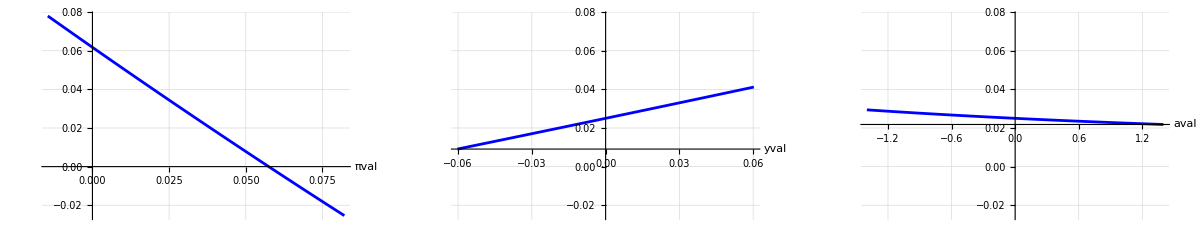

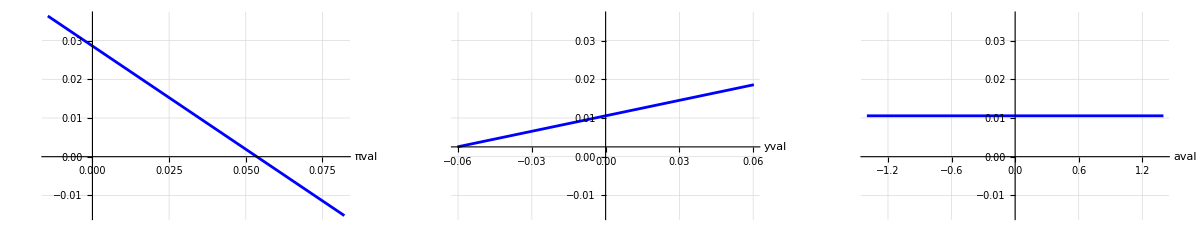

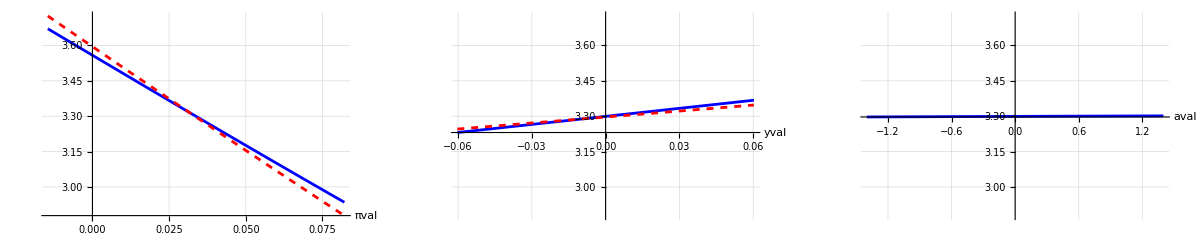

3.29925

```mathematica
(*mult is the quantile needed to cover the 99% conf. interval*)
mult=InverseCDF[NormalDistribution[0,1],0.995];

πminNew=πbar-mult√(σπ^2/(2 λπ))/.calibrationStock;
πmaxNew=πbar+mult√(σπ^2/(2 λπ))/.calibrationStock;
aminNew=0-mult√(σa^2/(2 λa))/.calibrationStock;
amaxNew=0+mult√(σa^2/(2 λa))/.calibrationStock;
yminNew=0-mult √(σy^2/(2 λy))/.calibrationStock;
ymaxNew=0+mult √(σy^2/(2 λy))/.calibrationStock;

replstates={ππ->πbar,a->0,y->0}/.calibration;
replstatesdiffa=replstates/. Rule[a,_]->Rule[a,-1.5];

g1=Plot[{μδN/.{ππ->πval}/.replstates},{πval,πminNew,πmaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g2=Plot[{μδN/.{y->yval}/.replstates},{yval,yminNew,ymaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g3=Plot[{μδN/.{a->aval}/.replstates},{aval,aminNew,amaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
ydata=Join[Cases[g1,Line[pts_]:>pts[[All,2]],Infinity],Cases[g2,Line[pts_]:>pts[[All,2]],Infinity],Cases[g3,Line[pts_]:>pts[[All,2]],Infinity]]//Flatten;
{ymin,ymax}={Min[ydata],Max[ydata]};
GraphicsRow[{Show[g1,PlotRange->{Automatic,{ymin,ymax}}],Show[g2,PlotRange->{Automatic,{ymin,ymax}}],Show[g3,PlotRange->{Automatic,{ymin,ymax}}]},ImageSize->Full]


g1=Plot[{rfN/.{ππ->πval}/.replstates},{πval,πminNew,πmaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g2=Plot[{rfN/.{y->yval}/.replstates},{yval,yminNew,ymaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g3=Plot[{rfN/.{a->aval}/.replstates},{aval,aminNew,amaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
ydata=Join[Cases[g1,Line[pts_]:>pts[[All,2]],Infinity],Cases[g2,Line[pts_]:>pts[[All,2]],Infinity],Cases[g3,Line[pts_]:>pts[[All,2]],Infinity]]//Flatten;
{ymin,ymax}={Min[ydata],Max[ydata]};
GraphicsRow[{Show[g1,PlotRange->{Automatic,{ymin,ymax}}],Show[g2,PlotRange->{Automatic,{ymin,ymax}}],Show[g3,PlotRange->{Automatic,{ymin,ymax}}]},ImageSize->Full]


PDratioN=Exp[Π[ππ[t],a[t],y[t]]]/.ChangeIto2/.replaceΠall//Simplify;
g1=Plot[{Log[PDratioN]/.{ππ->πval}/.replstates,Log[PDratioN]/.{ππ->πval}/.replstatesdiffa},{πval,πminNew,πmaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g2=Plot[{Log[PDratioN]/.{y->yval}/.replstates,Log[PDratioN]/.{y->yval}/.replstatesdiffa},{yval,yminNew,ymaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g3=Plot[{Log[PDratioN]/.{a->aval}/.replstates},{aval,aminNew,amaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
ydata=Join[Cases[g1,Line[pts_]:>pts[[All,2]],Infinity],Cases[g2,Line[pts_]:>pts[[All,2]],Infinity],Cases[g3,Line[pts_]:>pts[[All,2]],Infinity]]//Flatten;
{ymin,ymax}={Min[ydata],Max[ydata]};
GraphicsRow[{Show[g1,PlotRange->{Automatic,{ymin,ymax}}],Show[g2,PlotRange->{Automatic,{ymin,ymax}}],Show[g3,PlotRange->{Automatic,{ymin,ymax}}]},ImageSize->Full]

PISOL1/.replstates
```

Stock variance and risk premium

```mathematica
Stock=Exp[d[t]] Exp[Π[ππ[t],a[t],y[t]]];
Stockdiff={Diffusion[ItoD[Stock]/Stock,BrownianList->{Subscript[dB, 1],Subscript[dB, 2],Subscript[dB, 3],Subscript[dB, 4],Subscript[dB, 5]}]}/.ChangeIto2//FullSimplify
StockVar=(Stockdiff.Transpose[Stockdiff])[[1,1]]//FullSimplify
StockdiffNoDiv={Stockdiff[[1,1;;4]]};
StockRP=(StockdiffNoDiv.MPR)[[1,1]]//FullSimplify;

StockVarN=StockVar/.replaceΠall/.replrN/.ChangeIto2/.replrNbar/.replaceWCall/.calibrationStock;
StockRPN=StockRP/.replaceΠall/.replrN/.ChangeIto2/.replrNbar/.replaceWCall/.calibrationStock;
StockSRN=StockRPN/Sqrt[StockVarN];

rfN/.replstates
rfnominalN/.replstates

Print["The market risk premium for Table 4 (Model):"]
StockRPN/.replstates (*S&P500 RP=5.96% if fedfunds is rf; RP=6.32% if 1-month tbill is rf%*)

Print["The market return volatility for Table 4 (Model):"]
√StockVarN/.replstates (*S&P500 vol=14.90% if fedfunds is rf; vol=14.88% if 1-month tbill is rf%*)

StockSRN/.replstates
Log[PDratioN]/.replstates; (*S&P500 Log(PD)=3.61; Log(PE)=2.86; average(of the two)=3.235*)
PDratioN/.replstates (*S&P500 PD=40.15; PE=19.20*)
```

{{0,(calibfactorν (rNbar-rNt) λπ σa^2 Π^(0,1,0)[ππ,a,y])/(2 λa σπ)+σπ Π^(1,0,0)[ππ,a,y],σy Π^(0,0,1)[ππ,a,y],0,σd}}

σd^2+σy^2 (Π^(0,0,1)[ππ,a,y])^2+((calibfactorν (rNbar-rNt) λπ σa^2 Π^(0,1,0)[ππ,a,y])/(2 λa σπ)+σπ Π^(1,0,0)[ππ,a,y])^2

0.0105659

0.0443659

The market risk premium for Table 4 (Model):

0.0568938

The market return volatility for Table 4 (Model):

0.117778

0.483058

27.0923

```mathematica
replstates={ππ->πbar,a->0,y->0}/.calibration;
StockRPN/.replstates (*S&P500 RP=5.96% if fedfunds is rf; RP=6.32% if 1-month tbill is rf%*)
√StockVarN/.replstates (*S&P500 vol=14.90% if fedfunds is rf; vol=14.88% if 1-month tbill is rf%*)
```

0.0568938

0.117778

Stock variance and risk premium: equations as in the paper.

```mathematica
Stockdiffforpaper={Diffusion[ItoD[Stock]/Stock,BrownianList->{Subscript[dB, 1],Subscript[dB, 2],Subscript[dB, 3],Subscript[dB, 4],Subscript[dB, 5]}]}/.ChangeIto2/.calibfactorν->νa(2 λa)/σa^2//FullSimplify;
MPRforpaper;
StockdiffforpaperNoDiv={Stockdiffforpaper[[1,1;;4]]};
StockRPNforpaper=(StockdiffforpaperNoDiv.MPRforpaper)[[1,1]]//FullSimplify
StockVarforpaper=(Stockdiffforpaper.Transpose[Stockdiffforpaper])[[1,1]]//FullSimplify
```

(-1+θ) (-σy^2 WC^(0,0,1)[ππ,a,y] Π^(0,0,1)[ππ,a,y]-(((rNbar-rNt) λπ νa WC^(0,1,0)[ππ,a,y]+σπ^2 WC^(1,0,0)[ππ,a,y]) ((rNbar-rNt) λπ νa Π^(0,1,0)[ππ,a,y]+σπ^2 Π^(1,0,0)[ππ,a,y]))/σπ^2)

σd^2+σy^2 (Π^(0,0,1)[ππ,a,y])^2+(((rNbar-rNt) λπ νa Π^(0,1,0)[ππ,a,y])/σπ+σπ Π^(1,0,0)[ππ,a,y])^2

Risk premium as a function of a and ϕ (which varies from -rNbar to rNbar). Figure 5, top panels. To obtain the dashed lines, double the calibration of ν_a (see Footnote 12).

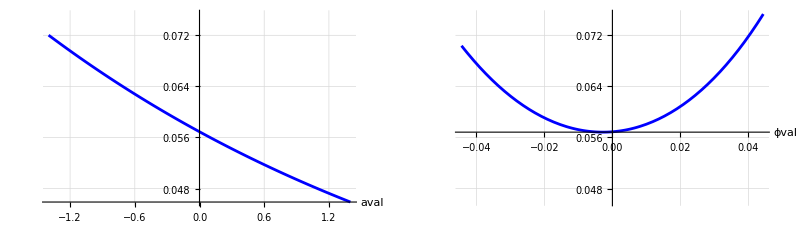

```mathematica
ϕminNew=-rNbar/.replrNbar/.replaceWCall/.calibration;
ϕmaxNew=-ϕminNew;

g1=Plot[{StockRPN/.replaceyWithϕ/.calibration/.{a->aval}/.replstates/.ϕ->0},{aval,aminNew,amaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g2=Plot[{StockRPN/.replaceyWithϕ/.calibration/.{ϕ->ϕval}/.replstates},{ϕval,ϕminNew,ϕmaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
ydata=Join[Cases[g1,Line[pts_]:>pts[[All,2]],Infinity],Cases[g2,Line[pts_]:>pts[[All,2]],Infinity]]//Flatten;
{ymin,ymax}={Min[ydata],Max[ydata]};
GraphicsRow[{Show[g1,PlotRange->{Automatic,{ymin,ymax}}],Show[g2,PlotRange->{Automatic,{ymin,ymax}}]},ImageSize->Full]
```

```mathematica
(* Export data for plots *)

GraphicsRow[{g1,g2,g3}];
datag1=Cases[g1,Line[pts_]:>pts,Infinity][[1]];
datag2=Cases[g2,Line[pts_]:>pts,Infinity][[1]];

formatData[data_]:=Map[N[Round[#,10^(-6)]]&,data,{2}]

(*Export["tabRPa.csv",formatData[datag1],"CSV"];
Export["tabRPphi.csv",formatData[datag2],"CSV"];*)
```

Vol as a function of a and ϕ (which varies from -rNbar to rNbar). Figure 5, bottom panels. To obtain the dashed lines, double the calibration of ν_a (see Footnote 12).

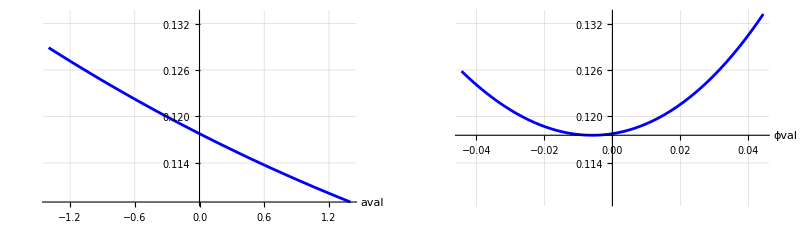

```mathematica
g1=Plot[{√StockVarN/.replaceyWithϕ/.calibration/.{a->aval}/.replstates/.ϕ->0},{aval,aminNew,amaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
g2=Plot[{√StockVarN/.replaceyWithϕ/.calibration/.{ϕ->ϕval}/.replstates},{ϕval,ϕminNew,ϕmaxNew},PlotStyle->{{Blue},{Red,Dashed}},GridLines->Automatic,AxesLabel->Automatic];
ydata=Join[Cases[g1,Line[pts_]:>pts[[All,2]],Infinity],Cases[g2,Line[pts_]:>pts[[All,2]],Infinity]]//Flatten;
{ymin,ymax}={Min[ydata],Max[ydata]};
GraphicsRow[{Show[g1,PlotRange->{Automatic,{ymin,ymax}}],Show[g2,PlotRange->{Automatic,{ymin,ymax}}]},ImageSize->Full]
```

```mathematica
(* Export data for plots *)

GraphicsRow[{g1,g2,g3}];
datag1=Cases[g1,Line[pts_]:>pts,Infinity][[1]];
datag2=Cases[g2,Line[pts_]:>pts,Infinity][[1]];

formatData[data_]:=Map[N[Round[#,10^(-6)]]&,data,{2}]

(*Export["tabVola.csv",formatData[datag1],"CSV"];
Export["tabVolphi.csv",formatData[datag2],"CSV"];*)
```

```mathematica
endTime=AbsoluteTime[];
duration=endTime-startTime;
Print["Total runtime: ",duration," seconds"];
```

Total runtime: 36.879625 seconds